```mathematica
Clear["Global`*"];
Needs["INVARIANT`"];
$HistoryLength=0;
```

## Simulation

### setup mesh and parameters

{Δ1→2,Δ2→2,Δ3→2,Gx_1111→1.,Gx_1122→0,Gx_1212→1.,Gp_1111→0.1,Gp_1122→0,Gp_1212→0.1,C_1111→2630.72,C_1122→787.953,C_1212→1039.29,β_11→-0.504477,β_1111→0.174591,β_1122→0.167076,γ_p→0.113603,Q_1111→0.00156177,Q_1122→0.00209644,Q_1212→0.00457593,γ_pc→-6.82245,α_xx→-0.141613,α_xxxx→0.117507,α_xxXX→-0.192626,α_xxyy→-0.26145,α_xxYY→-0.183314,γ_x5→-0.0826588,γ_xc→-5.76589,η_a1b2p3→7.45305,η_c1c2p3→-0.080697,η_a2b1p3→7.40847,γ_xp→0.149026}

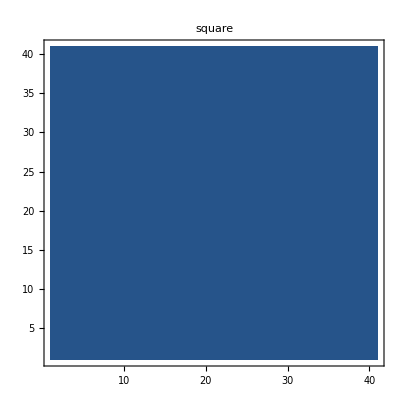
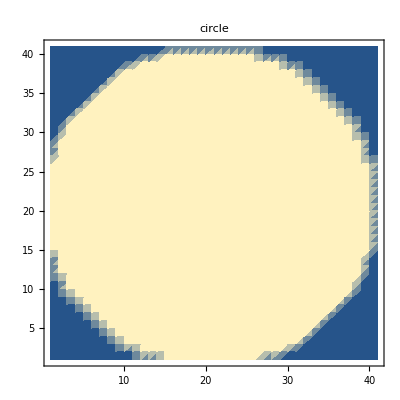
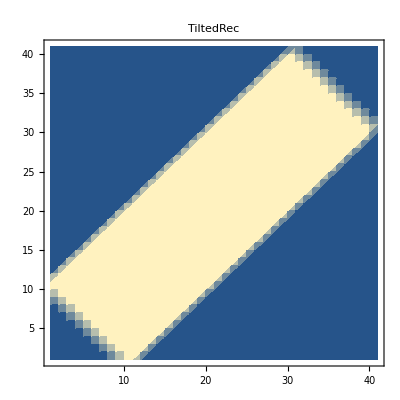
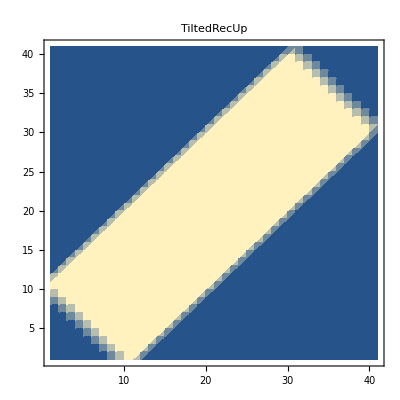
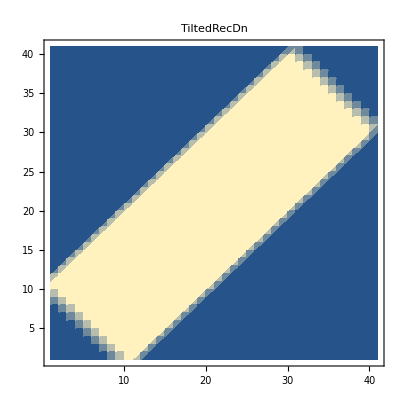
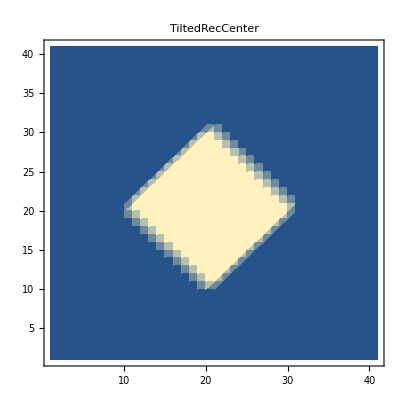
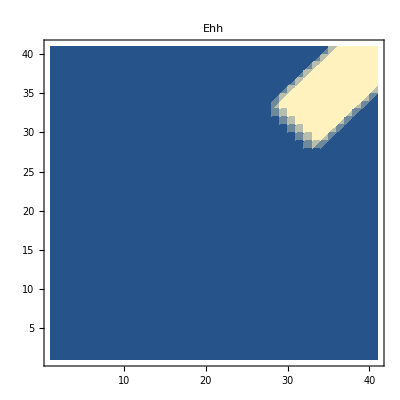
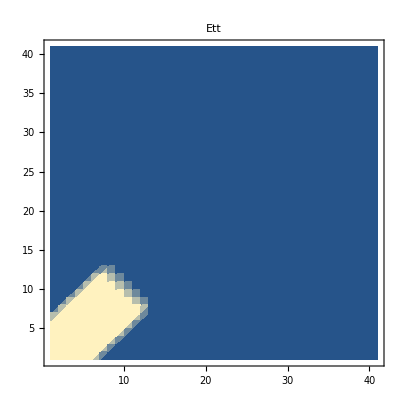

```mathematica
TempCoeff={Subscript[C,1111]->2630.720199808822,Subscript[C,1122]->787.9532029181885,Subscript[C,1212]->1039.2852937577954,Subscript[β,11]->-0.5044768267332222,Subscript[β,1111]->0.17459101764256235,Subscript[β,1122]->0.16707550949168,Subscript[γ,p]->0.11360338810072582,Subscript[Q,1111]->0.0015617734347307362,Subscript[Q,1122]->0.002096435259444331,Subscript[Q,1212]->0.0045759294858504366,Subscript[γ,pc]->-6.822450975792265,Subscript[α,xx]->-0.14161324961352054,Subscript[α,xxxx]->0.11750744312274372,Subscript[α,xxXX]->-0.19262613956826413,Subscript[α,xxyy]->-0.26144973824015766,Subscript[α,xxYY]->-0.1833140004264515,Subscript[γ,x5]->-0.08265877106249529,Subscript[γ,xc]->-5.765892474809912,Subscript[η,a1b2p3]->7.453047068990745,Subscript[η,c1c2p3]->-0.08069700048989199,Subscript[η,a2b1p3]->7.408472757634671,Subscript[γ,xp]->0.14902633780562038};
param=Join[{Δ1->2,Δ2->2,Δ3->2 ,Subscript[Gx, 1111]->1.0,Subscript[Gx, 1122]->0,Subscript[Gx, 1212]->1.0,Subscript[Gp, 1111]->0.1,Subscript[Gp, 1122]->0,Subscript[Gp, 1212]->0.1},TempCoeff]
case="random";
dir0="/home/paulchern/QMT/Boracites/Bora-5.3";
dir=dir0<>"/Bora-5.3-T"<>case<>"/";
Lx=41;Ly=41;Lz=2;NT=10;
MaskList=ListDensityPlot[Table[MeshMask[#,{Lx,Ly,Lz},x,y,1],{x,1,Lx},{y,1,Ly}]ᵀ,AspectRatio->Lx/Ly,PlotLabel->#]&/@{"square","circle","TiltedRec","TiltedRecUp","TiltedRecDn","TiltedRecCenter","Ehh","Ett","Enarrow1","Enarrow2","EnarrowVertical"}
```

### discretization

```mathematica
zbc=Dispatch[{Subscript[u, 3,x_,y_,Lz+1]:>Subscript[u, 3,x,y,1]}];
xbc=Dispatch[{Subscript[u, 3,Lx+1,y_,z_]:>Subscript[u, 3,1,y,z]}];
```

```mathematica
meshtype="square";
fDisc0=LandauInvariant["Discretized"];
fDisc = Sum[MeshMask[meshtype,{Lx,Ly,Lz},x,y,z]fDisc0, {x, Lx}, {y, Ly}, {z, Lz}]/.param//Expand;
Length[vars=Variables@fDisc]
```

62484

#### Read From QMT

```mathematica
minlist=Table[{ToExpression[#1],ToExpression[StringReplace[#2,"e"->"*10^"]]}&@@@Partition[StringSplit[Import[dir<>"Bora-5.3-T"<>case<>"."<>ToString[n]<>".txt"],{"\t","\n"}],2],{n,NT+2}];
sublist=Table[Flatten[{#1->#2}&@@@minlist[[n]]],{n,Length@minlist}];
pdata=GetOpTables[minlist,{Lx,Ly,Lz}];
```

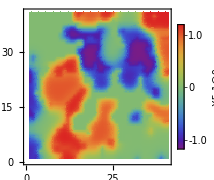
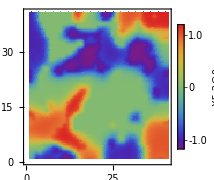
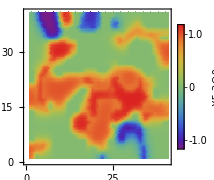
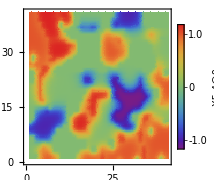
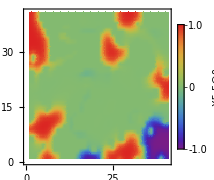
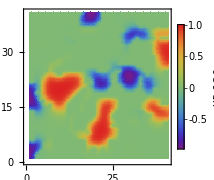
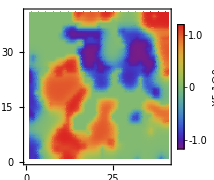
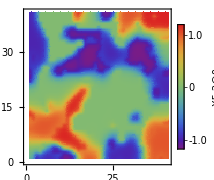
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
CompareOP[pdata,sublist,{1,2},{Lx,Ly,Lz},"separated"]
```

```mathematica
PathPlot[sublist,{1,6},19,1,param]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Minimize again

```mathematica
min=MinimizeBoracite[minlist[[1]],{Lx,Ly,Lz},fDisc,100000,"square",{},10000]
```

Minimizing without electric field.

Initializing minimization took 31.0162 seconds.

1
 |  |  |  |